```mathematica
ClearAll["Global`*"];
$Assumptions  = {σ ∈ Reals,σ > 0,ρ ∈ Reals,ρ>1,ϛ ∈ Reals, 𝕣 ∈ Reals, r ∈ Reals, 0 < ϛ < 1,ϕ ∈Reals};
(* 
r = log riskfree return (rate)
R = Exp[r] = riskfree return (factor) 
ℝ = Risky return (factor)
𝕣 = log risky return (rate)
𝕣tp1 ~ N(𝕣 - σ^2/2,σ^2)
σ = standard deviation of log risky return
ϕ = 𝕣-r = log equity premium (rate)
ϕtp1 ~ 𝒩(ϕ - σ^2/2,σ^2)
Φ = Exp[ϕ] = equity premium (factor)
ϛ = portfolio share in the risky asset
ℜ = R + (ℝ-R)ϛ = portfolio return
*)
```

```mathematica
(*
Campbell and Viceira show that 
ℜtp1 ≈ Exp[ϕtp1 ϛ + ϛ(1-ϛ)σ^2/2]
which implies that 
𝔼t[ℜtp1^(1-ρ)] ≈ Exp[(1-ρ)ϛ(1-ϛ)σ^2/2] 𝔼t[Exp[(1-ρ) ϕtp1 ϛ]]
≈ Exp[(1-ρ)ϛ(1-ϛ)σ^2/2] 𝔼t[Φtp1^((1-ρ)ϛ)]]
*)
𝔼tΦtp1Term = Integrate[Exp[(1-ρ)ϛ Log[Φ]] PDF[LogNormalDistribution[ϕ-σ^2/2,σ],Φ],{Φ,0,∞}]
```

ⅇ^(1/2 (-1+ρ) ϛ (-2 ϕ+σ^2 (1+(-1+ρ) ϛ)))

```mathematica
logE = Simplify[Log[𝔼tΦtp1Term]]
```

1/2 (-1+ρ) ϛ (-2 ϕ+σ^2 (1+(-1+ρ) ϛ))

```mathematica
Simpler4Sub = (1-ρ)(ϕ ϛ -ϛ(1-(1-ρ)ϛ)(σ^2/2));
Simpler5Sub = (1-ρ)(ϕ ϛ -ϛ(1-ϛ)(σ^2/2)-ρ ϛ^2(σ^2/2));
Simpler6Sub = -(ρ-1)(ϕ ϛ -ϛ(1-ϛ)(σ^2/2)-ρ ϛ^2(σ^2/2));
```

```mathematica
Simplify[logE == Simpler6Sub]
```

True

```mathematica
𝔼utp1 = Exp[(1-ρ)ϛ(1-ϛ)σ^2/2] Exp[logE];
log𝔼utp1 = Simplify[(1-ρ)ϛ(1-ϛ)σ^2/2 -(ρ-1)(ϕ ϛ -ϛ(1-ϛ)(σ^2/2)-ρ ϛ^2(σ^2/2))]
```

1/2 (-1+ρ) ϛ (-2 ϕ+ρ σ^2 ϛ)

```mathematica
Simplify[log𝔼utp1 == -(ρ-1) (ϕ ϛ - ϛ^2 ρ (σ^2/2))]
```

True

```mathematica
Assuming[{ϛ>0,ρ>0,ϕ>0},Maximize[{ϕ ϛ - ϛ^2 ρ (σ^2/2),ϕ>0,σ>0,ρ>0},ϛ]][[2]]
```

{ϛ→Piecewise[{{ϕ/(ρ σ^2), ϕ>0&&σ>0&&ρ>0}, {Indeterminate, True}}]}

```mathematica
𝔼uRaw[ϛ_,ρ_]:=-NIntegrate[(1+(Φ-1) ϛ)^(1-ρ) PDF[LogNormalDistribution[ϕ-σ^2/2,σ],Φ],{Φ,0,∞}];
ϛRawOpt[ρ_]:=ϛ /. FindMaximum[𝔼uRaw[ϛ,ρ],{ϛ,0.5}][[2]];
ϛApprox[ρ_]:=ϕ/(ρ σ^2);
```

```mathematica
σ=0.2;𝕣=0.08;r=0.00;ϕ=𝕣-r;
```

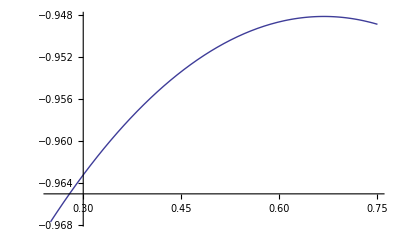

```mathematica
Plot[𝔼uRaw[ϛ,3],{ϛ,0.25,0.75}]
```

NIntegrate::inumr: The integrand 1.9947114020071635` ⅇ^-12.499999999999998` « 1 » « 1 »/Φ (1 + (-1 + Φ) ϛ)^1.0000612857142857` has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.`}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

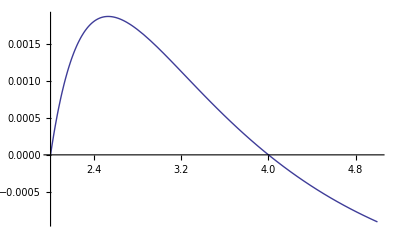

```mathematica
Plot[{ϛRawOpt[ρ]-ϛApprox[ρ]},{ρ,2,5}]
```